This notebook is provided as a companion resource for readers of Algebraic Functions by Dominic Milioto.  Commercial use of this notebook or its contents outside the context of the book is not permitted without the author’s permission.  The notebook is designed  with Mathematica version 13.2 and tested with version 15.  It contains stylesheet code to maintain the Report style, and classic bracketing [ [ ] ] for version 15.   See “Edit Stylesheet” and  notebook Initialization code for more information about these  changes.  

This notebook includes the test cases used in the chapter tutorials as well as additional cases intended for exploration and not exhaustively tested  and therefore may encounter software or numerical issues that can often be corrected by parameter adjustments.

# Chapter 12 Analyzing the Beta function for complex α and β ch12ComplexBeta.nb

## Section 1: Beta Test Cases

### complexBetaCase001

```mathematica
z1=1/2+1/2I;
z2=-1/2-1/2I;
theAlpha=1+z1;
theBeta=1+z2;

logF[z_,k_,j_]:=Exp[z1(Log[Abs[z]]+I (Arg[z]+2 k Pi))]Exp[z2(Log[Abs[1-z]]+I(Arg[1-z]+2 j Pi))];
H[z_,k_,j_]:=Exp[z1(Log[Abs[z]]+I (Arg[z]+2 k Pi))]Exp[z2(Log[Abs[1-z]]+I(Arg[1-z]+2 j Pi))];
reim=Im;
```

### complexBetaCase002

```mathematica
z1=1/10+1/20 I;
z2=-1/25-1/32 I;
theAlpha=1+z1;
theBeta=1+z2;

logF[z_,k_,j_]:=Exp[z1(Log[Abs[z]]+I (Arg[z]+2 k Pi))]Exp[z2(Log[Abs[1-z]]+I(Arg[1-z]+2 j Pi))];
H[z_,k_,j_]:=Exp[z1(Log[Abs[z]]+I (Arg[z]+2 k Pi))]Exp[z2(Log[Abs[1-z]]+I(Arg[1-z]+2 j Pi))];
reim=Im;
```

### complexBetaCase003

```mathematica
z1=1/75+1/75 I;
z2=-1/75-1/75 I;
theAlpha=1+z1;
theBeta=1+z2;

logF[z_,j_,k_]:=Exp[z1(Log[Abs[z]]+I (Arg[z]+2 j Pi))]Exp[z2(Log[Abs[1-z]]+I(Arg[1-z]+2 k Pi))];
H[z_,j_,k_]:=Exp[z1(Log[Abs[z]]+I (Arg[z]+2 j Pi))]Exp[z2(Log[Abs[1-z]]+I(Arg[1-z]+2 k Pi))];

reim=Im;
testJ=-3;
testK=4;
H[1+2 I,testJ,testK-1]//N
H[1+2 I,testJ+1,testK]//N
```

1.42754-0.717012 ⅈ

1.42754-0.717012 ⅈ

### complexBetaCase004

```mathematica
z1=1/75+1/75 I;
z2=-1/75-1/75 I;
theAlpha=1+z1;
theBeta=1+z2;

logF[z_,k_,j_]:=Exp[z1(Log[Abs[z]]+I (Arg[z]+2 k Pi))]Exp[z2(Log[Abs[1-z]]+I(Arg[1-z]+2 j Pi))];
H[z_,k_,j_]:=Exp[z1(Log[Abs[z]]+I (Arg[z]+2 k Pi))]Exp[z2(Log[Abs[1-z]]+I(Arg[1-z]+2 j Pi))];
reim=Im;
```

### complexBetaCase005

```mathematica
z1=1/10+1/2 I;
z2=-1/25-1/32 I;
theAlpha=1+z1;
theBeta=1+z2;

logF[z_,k_,j_]:=Exp[z1(Log[Abs[z]]+I (Arg[z]+2 k Pi))]Exp[z2(Log[Abs[1-z]]+I(Arg[1-z]+2 j Pi))];
H[z_,k_,j_]:=Exp[z1(Log[Abs[z]]+I (Arg[z]+2 k Pi))]Exp[z2(Log[Abs[1-z]]+I(Arg[1-z]+2 j Pi))];
reim=Re;
```

### complexBetaCase006

```mathematica
z1=1/4+2/3I;
z2=1/4+2/3 I;
theAlpha=1+z1;
theBeta=1+z2;

logF[z_,k_,j_]:=Exp[z1(Log[Abs[z]]+I (Arg[z]+2 k Pi))]Exp[z2(Log[Abs[1-z]]+I(Arg[1-z]+2 j Pi))];
H[z_,k_,j_]:=Exp[z1(Log[Abs[z]]+I (Arg[z]+2 k Pi))]Exp[z2(Log[Abs[1-z]]+I(Arg[1-z]+2 j Pi))];
reim=Im;
```

## Illustration of branches of H(z,j,k)

```mathematica
plot00=ParametricPlot3D[{Re@z,Im@z,reim@H[z,0,0]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Red},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
plot00B=ParametricPlot3D[{Re@z,Im@z,reim@H[z,0,0]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Red},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
Show[{plot00,plot00B},PlotRange->All]
```

-Graphics3D-

```mathematica
contourF[t_]:=0.75 Exp[I t];
tStart=Pi/2;
tEnd=8Pi/6;
wStart0=Log[contourF[tStart]];
wStart1=Log[1-contourF[tStart]];

 log0Deriv=w'[t]==(1/contourF[t] D[contourF[t],t]);

log0Sol=NDSolveValue[{log0Deriv,w[tStart]==wStart0},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->1/1000];
log0WEnd=log0Sol[tEnd];
(*
 do log around z=1 log1Deriv,log1WStart,log1Sol,log1WEnd
*)
log1Deriv=w'[t]==(-1/(1-contourF[t]) D[contourF[t],t]);
log1Sol=NDSolveValue[{log1Deriv,w[tStart]==wStart1},w,{t,tStart,tEnd}];
log1WEnd=log1Sol[tEnd];
(*
 now compute integral over leg 
*)
 contourBetaF[t_]:=(Exp[z1 log0Sol[t]] Exp[z2 log1Sol[t]]);
wVal=contourBetaF[tStart+0.5]
wPointG=Graphics3D@{PointSize[0.025],Yellow,Point@{Re@contourF[tStart],Im@contourF[tStart],reim@wVal}};


{contourBF2,theContourPlot2,cVal2,pWEnd2,pWEnd,tractPoints2}=getLogContourTract[contour1,tStart1,tEnd1,Blue,wStart0,wStart1,z1,z2,reim];
tractArrowG2=Graphics3D@{Arrowheads[0.02],Black,Thickness[0.005],Arrow[BSplineCurve[tractPoints2]]};
Show[{plot00,plot00B,wPointG,tractArrowG2},PlotRange->All]
```

0.95767+0.0232635 ⅈ

-Graphics3D-

```mathematica
reim=Im;
theJ=0;
theK=0; plot1=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Red},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
plot2=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Red},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];

plot3=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Blue},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
plot4=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Blue},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];

plot5=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Green},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
plot6=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Green},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];

plot7=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ+1,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Orange},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
plot8=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ+1,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Orange},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];

plot9=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ+1,theK]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Yellow},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
plot10=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ+1,theK]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Yellow},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];



Show[{plot1,plot2,plot3,plot4,plot5,plot6,plot7,plot8,plot9,plot10},PlotRange->All,ImageSize->300,BoxRatios->{1,1,2}]
```

-Graphics3D-

```mathematica
tractPoints2//N
```

{{0.,0.75,0.0355112},{-0.194114,0.724444,0.0360648},{-0.375,0.649519,0.0368889},{-0.53033,0.53033,0.0379567},{-0.649519,0.375,0.0392505},{-0.724444,0.194114,0.0407605},{-0.75,0.,0.0424837},{-0.724444,-0.194114,0.0444244},{-0.649519,-0.375,0.046594},{-0.53033,-0.53033,0.0490134},{-0.375,-0.649519,0.0517154}}

```mathematica
contour[t_]:=1+0.75 Exp[I t];
tStart=Pi/2;
tEnd=-Pi/6;
wStart0=Log[contour[tStart]];
wStart1=Log[1-contour[tStart]];
{contourBF,theContourPlot,cVal,purpleLog0WEnd,purpleLog1WEnd,tractPoints}=getLogContourTract[contour,tStart,tEnd,Red,wStart0,wStart1,z1,z2,reim];
tractArrowG=Graphics3D@{Arrowheads[0.02],Green,Thickness[0.005],Arrow[BSplineCurve[tractPoints]]};

contour1[t_]:=0.75 Exp[I t];
tStart1=Pi/2;
tEnd1=8Pi/6;
wStart0=Log[contour1[tStart1]];

wStart1=Log[1-contour1[tStart1]];
{contourBF2,theContourPlot2,cVal2,pWEnd2,pWEnd,tractPoints2}=getLogContourTract[contour1,tStart1,tEnd1,Blue,wStart0,wStart1,z1,z2,reim];
tractArrowG2=Graphics3D@{Arrowheads[0.02],Black,Thickness[0.005],Arrow[BSplineCurve[tractPoints2]]};

wStartG=Graphics3D@{Yellow,PointSize[0.05],Point@tractPoints2[[1]]};

contour3[t_]:=0.75 Exp[I t];
tStart3=-Pi/2;
tEnd3=-5 Pi/4;
wStart0=Log[contour3[tStart3]];
wStart1=Log[1-contour3[tStart3]];
{contourBF3,theContourPlot3,cVal3,pWEnd3,pWEnd,tractPoints3}=getLogContourTract[contour3,tStart3,tEnd3,Green,wStart0,wStart1,z1,z2,reim];
tractArrowG3=Graphics3D@{Arrowheads[0.03],Black,Thickness[0.005],Arrow[BSplineCurve[tractPoints3]]};

contour4[t_]:=1+0.75 Exp[I t];
tStart4=-Pi/2;
tEnd4=Pi/3;
wStart0=Log[contour4[tStart4]];
wStart1=Log[1-contour4[tStart4]];
{contourBF4,theContourPlot4,cVal4,pWEnd4,pWEnd,tractPoints4}=getLogContourTract[contour4,tStart4,tEnd4,Black,wStart0,wStart1,z1,z2,reim];
tractArrowG4=Graphics3D@{Arrowheads[0.03],Black,Thickness[0.005],Arrow[BSplineCurve[tractPoints4]]};

sing1G=Graphics3D@{PointSize[0.015],Blue,Point@{0,0,0}};
sing2G=Graphics3D@{PointSize[0.015],Blue,Point@{1,0,0}};

tempPlot=Show[{plot00,plot00B,tractArrowG,tractArrowG2,tractArrowG3,tractArrowG4,sing1G,sing2G},PlotRange->All];
pRange=PlotRange[tempPlot];
line1G=Graphics3D@{Thickness[0.005],Line[{{0,0,pRange[[3,1]]},{0,0,pRange[[3,2]]}}]};
line2G=Graphics3D@{Thickness[0.005],Line[{{1,0,pRange[[3,1]]},{1,0,pRange[[3,2]]}}]};

blackZ=1+ Exp[-Pi I/3]//N
blackW=reim@logF[blackZ,0,0]//N
blackText3D=Graphics3D@Text[Style["k+1",Bold,Black,14],Join[ReIm@blackZ,{blackW}]];

greenZ=1.2Exp[-2Pi I/3]//N
greenW=reim@logF[greenZ,0,0]//N
greenText3D=Graphics3D@Text[Style["j-1",Bold,Black,14],Join[ReIm@greenZ,{greenW}]];

blueZ=Exp[2Pi I/3]//N
blueW=reim@logF[blueZ,0,0]//N
blueText3D=Graphics3D@Text[Style["j+1",Bold,Black,14],Join[ReIm@blueZ,{blueW}]];

 redZ=1+Exp[Pi I/3]//N
redW=reim@logF[redZ,0,0]//N
redText3D=Graphics3D@Text[Style["k-1",Bold,Black,14],Join[ReIm@redZ,{redW}]];

Show[{plot1,plot2,blackText3D,greenText3D,blueText3D,redText3D,wStartG,(*logF0M1,logF0M1B,logF10,logF10B,logFM10,logFM10B,*)tractArrowG,tractArrowG2,tractArrowG3,tractArrowG4,sing1G,sing2G},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,(*FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},*)AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},PlotRange->All]
```

1.5-0.866025 ⅈ

-0.0287686

-0.6-1.03923 ⅈ

-0.0430233

-0.5+0.866025 ⅈ

0.0264386

1.5+0.866025 ⅈ

0.0410695

-Graphics3D-

```mathematica
(*
 do (1,0)
*)

  plotBlue=ParametricPlot3D[{Re@z,Im@z,reim@H[z,1,0]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Blue},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
plotBlueB=ParametricPlot3D[{Re@z,Im@z,reim@H[z,1,0]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Blue},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
Show[{plot00,plot00B,plotBlue,plotBlueB,blackText3D,greenText3D,blueText3D,redText3D,(*logF0M1,logF0M1B,logF10,logF10B,logFM10,logFM10B,*)tractArrowG,tractArrowG2,tractArrowG3,tractArrowG4,sing1G,sing2G},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,(*FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},*)AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},PlotRange->All]
```

-Graphics3D-

```mathematica
(*
 do (0,-1)
*)

   plotGreen=ParametricPlot3D[{Re@z,Im@z,reim@H[z,0,-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Magenta},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
plotGreenB=ParametricPlot3D[{Re@z,Im@z,reim@H[z,0,-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Magenta},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
Show[{plot00,plot00B,plotBlue,plotBlueB,plotGreen,plotGreenB,blackText3D,greenText3D,blueText3D,redText3D,(*logF0M1,logF0M1B,logF10,logF10B,logFM10,logFM10B,*)tractArrowG,tractArrowG2,tractArrowG3,tractArrowG4,sing1G,sing2G},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,(*FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},*)AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},PlotRange->All]
```

-Graphics3D-

```mathematica
(*
 do (-1,0)
*)

   plotOrange=ParametricPlot3D[{Re@z,Im@z,reim@H[z,-1,0]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Green},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
plotOrangeB=ParametricPlot3D[{Re@z,Im@z,reim@H[z,-1,0]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Green},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
Show[{plot00,plot00B,plotBlue,plotBlueB,plotOrange,plotOrangeB,blackText3D,greenText3D,blueText3D,redText3D,(*logF0M1,logF0M1B,logF10,logF10B,logFM10,logFM10B,*)tractArrowG,tractArrowG2,tractArrowG3,tractArrowG4,sing1G,sing2G},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,(*FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},*)AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},PlotRange->All]
```

-Graphics3D-

```mathematica
(*
 do (0,1)
*)

   plotPurple=ParametricPlot3D[{Re@z,Im@z,reim@H[z,0,1]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Purple},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
plotPurpleB=ParametricPlot3D[{Re@z,Im@z,reim@H[z,0,1]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Purple},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];

finalBranchPlot=Show[{plot00,plot00B,plotBlue,plotBlueB,plotGreen,plotGreenB,plotOrange,plotOrangeB,plotPurple,plotPurpleB,blackText3D,greenText3D,blueText3D,redText3D,(*logF0M1,logF0M1B,logF10,logF10B,logFM10,logFM10B,*)tractArrowG,tractArrowG2,tractArrowG3,tractArrowG4,sing1G,sing2G},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,(*FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},*)AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},PlotRange->All]
```

-Graphics3D-

```mathematica
theContourPlots={blueLogPlot,purpleLogPlot,greenLogPlot,redLogPlot,blackLogPlot,yellowLogPlot,orangeLogPlot,brownLogPlot};
```

```mathematica
Show[{plot00,plot00B,plotBlue,plotBlueB,plotGreen,plotGreenB,plotOrange,plotOrangeB,plotPurple,plotPurpleB,blackText3D,greenText3D,blueText3D,redText3D,theContourPlots,(*logF0M1,logF0M1B,logF10,logF10B,logFM10,logFM10B,*)tractArrowG,tractArrowG2,tractArrowG3,tractArrowG4,sing1G,sing2G},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,(*FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},*)AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},PlotRange->All]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,{blueLogPlot,purpleLogPlot,greenLogPlot,redLogPlot,blackLogPlot,yellowLogPlot,orangeLogPlot,brownLogPlot},-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},AxesEdge→{{-1,-1},{1,-1},{-1,-1}},Axes→True,AxesLabel→{Re(z),Im(z),Im(w)},FaceGridsStyle→Directive[GrayLevel[0],Dashing[{0,Small}]],BoxRatios→{1,1,1},PlotRange→All]

```mathematica
Show[{plot00,plot00B,blackText3D,greenText3D,blueText3D,redText3D,tractArrowG,tractArrowG2,tractArrowG3,tractArrowG4,sing1G,sing2G},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->None,Boxed->False,PlotRange->finalPlotRange]
```

-Graphics3D-

## Section 2: Create general Pochhammer contour for complex exponents

```mathematica
(*
  general pochhammer contour
*)

contourArray={};
pocR1=1/3;
pocR2=1/2;
(*
 do blue contour
*)
 blueContourF[t_]:=(pocR2 I)(1-t)+(1+pocR2 I) t;
blueStartT=0;
blueEndT=1;
blueArrowG=Graphics@{Arrowheads[0.025],Arrow[{ReIm@blueContourF[0.1],ReIm@blueContourF[0.15]}]};
blueContourPlot=ParametricPlot[ReIm@blueContourF[t],{t,blueStartT,blueEndT},AxesOrigin->{0,0},PlotRange->1.5,PlotStyle->{Thickness[0.0025],Blue}];

AppendTo[contourArray,{blueContourF,blueStartT,blueEndT}];
  (*
 do purple contour
*)
 purpleContourF[t_]:=1+pocR2 Exp[I(Pi/2(1-t)+(-Pi/2) t)];
purpleStartT=0;
purpleEndT=1;
purpleContourPlot=ParametricPlot[ReIm@purpleContourF[t],{t,purpleStartT,purpleEndT},PlotStyle->{Thickness[0.0025],Purple},PlotRange->2];

 (* 
 green contour
*)

greenStartT=0;
greenEndT=1;
greenContourF[t_]:=(1-pocR2 I)(1-t)+pocR1 I t;
greenArrowG=Graphics@{Arrowheads[0.025],Arrow[{ReIm@greenContourF[0.1],ReIm@greenContourF[0.15]}]};
greenContourPlot=ParametricPlot[ReIm@greenContourF[t],{t,greenStartT,greenEndT},PlotStyle->{Thickness[0.0025],Darker@Green}];
(*
 do red contour
*)
redContourF[t_]:=pocR1 Exp[I(Pi/2(1-t)+3 Pi/2 t)];
redStartT=0;
redEndT=1;
redContourPlot=ParametricPlot[ReIm@redContourF[t],{t,redStartT,redEndT},PlotStyle->{Thickness[0.0025],Red}];
(*
 do black contour
*)
blackContourF[t_]:=-pocR1 I(1-t)+(1-pocR1 I) t;
blackStartT=0;
blackEndT=1;
blackArrowG=Graphics@{Black,Arrowheads[0.025],Arrow[{ReIm@blackContourF[0.1],ReIm@blackContourF[0.2]}]};
blackContourPlot=ParametricPlot[ReIm@blackContourF[t],{t,blackStartT,blackEndT},PlotStyle->{Thickness[0.0025],Black}];
(*
 do yellow contour
*)
yellowContourF[t_]:=1+pocR1 Exp[I(-Pi/2(1-t)+Pi/2 t)];
yellowStartT=0;
yellowEndT=1;
yellowContourPlot=ParametricPlot[{Re@z,Im@z}/.z->yellowContourF[t],{t,yellowStartT,yellowEndT},PlotStyle->{Thickness[0.0025],Darker@Yellow}];
(*
 do orange contour
*)
 orangeContourF[t_]:=(1+pocR1 I)(1-t)+(-pocR2 I)t
orangeStartT=0;
orangeEndT=1;
orangeArrowG=Graphics@{Black,Arrowheads[0.025],Arrow[{ReIm@orangeContourF[0.1],ReIm@orangeContourF[0.15]}]};
(*orangeContourF[x_]:=theSlope(x-ptSol[[ptIndex,1]])+ptSol[[ptIndex,2]];*)
orangeContourPlot=ParametricPlot[ReIm@orangeContourF[t],{t,orangeStartT,orangeEndT},PlotStyle->{Thickness[0.0025],Orange}];
(*
 do brown contour
*)
brownStartT=0;
brownEndT=1;
 brownContourF[t_]:=pocR2 Exp[(3Pi/2) I(1-t)+(Pi/2 I(t))];
brownContourPlot=ParametricPlot[ReIm@brownContourF[t],{t,0,1},PlotStyle->{Thickness[0.0025],Brown}];
zeroPointG=Graphics@{Blue,PointSize[0.015],Blue,Point[{0,0}]};
onePointG=Graphics@{Blue,PointSize[0.015],Blue,Point[{1,0}]};
```

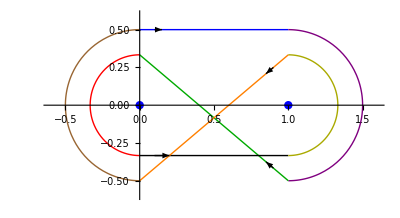

Precision of log0Sol: 30.

Precision of log1Sol: 30.

```mathematica
Show[{blueContourPlot,purpleContourPlot,greenContourPlot,redContourPlot,blackContourPlot,yellowContourPlot,orangeContourPlot,brownContourPlot,blueArrowG,greenArrowG,blackArrowG,orangeArrowG,zeroPointG,onePointG},PlotRange->{{-0.6,1.6},{-0.6,0.6}}]
```

## Section 3: Integrating over Pochhammer contour using General contour

```mathematica
selectedJ=0;
selectedK=0;


startWP=30; (* working precision *)
startAC=15; (* accuracy goal *)

Print["Blue contour"];
 blueLog0WStart=Log[blueContourF[0]]+2 Pi I selectedJ;
blueLog1WStart=Log[1-blueContourF[0]]+2 Pi I selectedK;
{contourBetaF,blueLogPlot,blueContourVal,blueLog0WEnd,blueLog1WEnd}=getLogContour[blueContourF,0,1,Blue,blueLog0WStart,blueLog1WStart,z1,z2,reim,"wp"->startWP,"ag"->startWP];
Print["blueContourVal: ",blueContourVal//N];
val1=logF[blueContourF[1],0,0];
val2=contourBetaF[1];
Print["Accuracy of contourBetaF[1]: ",Abs[val1-val2]];

purpleLog0WStart=blueLog0WEnd;
purpleLog1WStart=blueLog1WEnd;
nextWP=Floor@Precision@purpleLog0WStart;
Print["Purple contour"];
{contourBetaF,purpleLogPlot,purpleContourVal,purpleLog0WEnd,purpleLog1WEnd}=getLogContour[purpleContourF,0,1,Purple,purpleLog0WStart,purpleLog1WStart,z1,z2,reim,"wp"->nextWP,"ag"->nextWP];
val1=logF[purpleContourF[1],0,-1];
val2=contourBetaF[1];
Print["Accuracy of purple contourBetaF[1]: ",Abs[val1-val2]];


 greenLog0WStart=purpleLog0WEnd;
greenLog1WStart=purpleLog1WEnd;
nextWP=Floor@Precision@greenLog0WStart;
Print["Green contour"];
{contourBetaF,greenLogPlot,greenContourVal,greenLog0WEnd,greenLog1WEnd}=getLogContour[greenContourF,0,1,Darker@Green,greenLog0WStart,greenLog1WStart,z1,z2,reim,"wp"->nextWP,"ag"->nextWP];
val1=logF[greenContourF[1],0,-1];
val2=contourBetaF[1];
Print["Accuracy of green contourBetaF[1]: ",Abs[val1-val2]];


  redLog0WStart=greenLog0WEnd;
redLog1WStart=greenLog1WEnd;
nextWP=Floor@Precision@redLog0WStart;
Print["Red contour"];
{contourBetaF,redLogPlot,redContourVal,redLog0WEnd,redLog1WEnd}=getLogContour[redContourF,0,1,Darker@Red,redLog0WStart,redLog1WStart,z1,z2,reim,"wp"->nextWP,"ag"->nextWP];
val1=logF[redContourF[1],1,-1];
val2=contourBetaF[1];
Print["Accuracy of red contourBetaF[1]: ",Abs[val1-val2]];


blackLog0WStart=redLog0WEnd;
blackLog1WStart=redLog1WEnd;
nextWP=Floor@Precision@blackLog0WStart;
Print["Black contour"];
{contourBetaF,blackLogPlot,blackContourVal,blackLog0WEnd,blackLog1WEnd}=getLogContour[blackContourF,0,1,Darker@Black,blackLog0WStart,blackLog1WStart,z1,z2,reim,"wp"->nextWP,"ag"->nextWP];
val1=logF[blackContourF[1],1,-1];
val2=contourBetaF[1];
Print["Accuracy of black contourBetaF[1]: ",Abs[val1-val2]];

yellowLog0WStart=blackLog0WEnd;
yellowLog1WStart=blackLog1WEnd;
nextWP=Floor@Precision@yellowLog0WStart;
Print["Yellow contour"];
{contourBetaF,yellowLogPlot,yellowContourVal,yellowLog0WEnd,yellowLog1WEnd}=getLogContour[yellowContourF,0,1,Yellow,yellowLog0WStart,yellowLog1WStart,z1,z2,reim,"wp"->nextWP,"ag"->nextWP];
val1=logF[yellowContourF[1],1,0];
val2=contourBetaF[1];
Print["Accuracy of yellow contourBetaF[1]: ",Abs[val1-val2]];



orangeLog0WStart=yellowLog0WEnd;
orangeLog1WStart=yellowLog1WEnd;
nextWP=Floor@Precision@orangeLog1WStart;
Print["Orange contour"];
{contourBetaF,orangeLogPlot,orangeContourVal,orangeLog0WEnd,orangeLog1WEnd}=getLogContour[orangeContourF,0,1,Orange,orangeLog0WStart,orangeLog1WStart,z1,z2,reim,"wp"->nextWP,"ag"->nextWP];
val1=logF[orangeContourF[1],1,0];
val2=contourBetaF[1];
Print["Accuracy of orange contourBetaF[1]: ",Abs[val1-val2]];



brownLog0WStart=orangeLog0WEnd;
brownLog1WStart=orangeLog1WEnd;
nextWP=Floor@Precision@brownLog0WStart;

{contourBetaF,brownLogPlot,brownContourVal,brownLog0WEnd,brownLog1WEnd}=getLogContour[brownContourF,0,1,Brown,brownLog0WStart,brownLog1WStart,z1,z2,reim,"wp"->nextWP,"ag"->nextWP];
val1=logF[brownContourF[1],0,0];
val2=contourBetaF[1];
Print["Accuracy of brown contourBetaF[1]: ",Abs[val1-val2]];

Print["Brown contour"];

 contourVal=blueContourVal+purpleContourVal+greenContourVal+redContourVal+blackContourVal+yellowContourVal+orangeContourVal+brownContourVal;
Print["Precision of contourVal: ",Precision@contourVal];
theAlpha=1+z1;
theBeta=1+z2;

contourValue=contourVal/(Exp[2 Pi I selectedJ theAlpha]Exp[2 Pi I selectedK theBeta](1-Exp[2 Pi I theAlpha])(1-Exp[
-2Pi I theBeta ]));
Print["Contour value: ",contourValue];
betaValue=Beta[theAlpha,theBeta];
Print["Beta function value: ",N[betaValue,21]];
Print["Error: ",Abs[contourValue-betaValue]];
```

Blue contour

Precision of log0Sol: 30.

Precision of log1Sol: 30.

blueContourVal: 0.976909+0.0226064 ⅈ

Accuracy of contourBetaF[1]: 1.05600149403578×10^-16

Purple contour

Precision of log0Sol: 29.

Precision of log1Sol: 29.

Accuracy of purple contourBetaF[1]: 8.906708960068×10^-17

Green contour

Precision of log0Sol: 28.

Precision of log1Sol: 28.

Accuracy of green contourBetaF[1]: 3.0537071211944×10^-15

Red contour

Precision of log0Sol: 27.

Precision of log1Sol: 27.

Accuracy of red contourBetaF[1]: 1.10473342317×10^-15

Black contour

Precision of log0Sol: 26.

Precision of log1Sol: 26.

Accuracy of black contourBetaF[1]: 1.124726808429×10^-13

Yellow contour

Precision of log0Sol: 25.

Precision of log1Sol: 25.

Accuracy of yellow contourBetaF[1]: 6.04212373801×10^-14

Orange contour

Precision of log0Sol: 24.

Precision of log1Sol: 24.

Accuracy of orange contourBetaF[1]: 3.78066365392×10^-13

Precision of log0Sol: 23.

Precision of log1Sol: 23.

Accuracy of brown contourBetaF[1]: 4.6787710447×10^-13

Brown contour

Precision of contourVal: 21.0843

Contour value: 0.999999762115229629359+0.00058486205802839163 ⅈ

Beta function value: 0.999999760552718903945+0.00058486535739093587 ⅈ

Error: 3.65064829385×10^-9

### Log plot with pochhammer contour for testCase0002

```mathematica
theJ=selectedJ;
theK=selectedK; plot1=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Blue},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
plot2=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Blue},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];

plot3=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Red},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
plot4=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Red},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];

plot5=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Red},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
plot6=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Red},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];

plot7=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ+1,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Green},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
plot8=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ+1,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Green},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];

plot9=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ+1,theK]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Brown},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
plot10=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ+1,theK]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.5],Brown},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
```

```mathematica
logPlot=Show[{(*plot1,*)plot2,plot3,plot4,plot5,plot6,plot7,plot8,plot9,plot10,blueLogPlot,purpleLogPlot,greenLogPlot,redLogPlot,blackLogPlot,orangeLogPlot,brownLogPlot,yellowLogPlot},PlotRange->All,ImageSize->400,BoxRatios->{1,1,1.5}]
```

-Graphics3D-

## Section 4: Interactive 3D viewer

```mathematica
branchColorTable
```

{{1,RGBColor[1, 0, 0]},{2,RGBColor[0, 0, 1]},{3,RGBColor[0, Rational[2, 3], 0]},{4,RGBColor[Rational[2, 3], Rational[2, 3], 0]},{5,RGBColor[0.5, 0, 0.5]},{6,RGBColor[1, 0.5, 0]},{7,RGBColor[1, 0, 1]},{8,RGBColor[1, 0.5, 0.5]},{9,RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786]},{10,RGBColor[1., 0.7215686274509804, 0.2196078431372549]},{11,RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883]},{12,RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843]},{13,RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882]},{14,RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078]},{15,RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355]},{16,RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862]},{17,RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765]},{18,RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373]},{19,RGBColor[0.803921568627451, 0.30980392156862746, 0.07058823529411765]},{20,RGBColor[1., 0.7254901960784313, 0.09411764705882353]},{21,RGBColor[0.9568627450980393, 0.796078431372549, 0.13725490196078433]},{22,RGBColor[0.9529411764705882, 0.9803921568627451, 0.5725490196078431]},{23,RGBColor[0.4117647058823529, 0.592156862745098, 0.4]},{24,RGBColor[0.30980392156862746, 0.47058823529411764, 0.34509803921568627]},{25,RGBColor[0.2980392156862745, 0.28627450980392155, 0.5490196078431373]},{26,RGBColor[0.27058823529411763, 0.1843137254901961, 0.3764705882352941]},{27,RGBColor[0.8784313725490196, 0.10196078431372549, 0.20784313725490197]},{28,RGBColor[0.8, 0.058823529411764705, 0.07450980392156863]},{29,RGBColor[1., 0.796078431372549, 0.2627450980392157]},{30,RGBColor[0.9215686274509803, 0.8862745098039215, 0.592156862745098]},{31,RGBColor[0.9607843137254902, 0.9176470588235294, 0.00784313725490196]},{32,RGBColor[0.1803921568627451, 0.06274509803921569, 0.5803921568627451]},{33,RGBColor[0.1803921568627451, 0.011764705882352941, 0.3333333333333333]},{34,RGBColor[0.5294117647058824, 0.40784313725490196, 0.6392156862745098]},{35,RGBColor[0.7372549019607844, 0.18823529411764706, 0.3411764705882353]},{36,RGBColor[0.7843137254901961, 0.07058823529411765, 0.23137254901960785]},{37,RGBColor[0.9058823529411765, 0., 0.0784313725490196]},{38,RGBColor[0.797253, 0.904982, 0.410498]},{39,RGBColor[0.934691, 0.945708, 0.75346]},{40,RGBColor[0.769879, 0.92369, 0.977371]},{41,RGBColor[1, 0.566415, 0.0386511]},{42,RGBColor[1, 1, 0.4]},{43,RGBColor[1, 0.784756, 0.323308]},{44,RGBColor[0.909499, 0.582605, 0.44213]},{45,RGBColor[0.621866, 0.909026, 0.965408]},{46,RGBColor[1, 0.542397, 0.309712]},{47,RGBColor[0.645075, 0.644968, 0.978851]},{48,RGBColor[0.755657, 0.61117, 0.154498]},{49,RGBColor[0.4, 0.10196078431372549, 0.]},{50,RGBColor[0.9803921568627451, 0.807843137254902, 0.7333333333333333]},{51,RGBColor[0.7490196078431373, 0.43529411764705883, 0.24705882352941178]},{52,RGBColor[0.8235294117647058, 0.6039215686274509, 0.34901960784313724]},{53,RGBColor[0.4745098039215686, 0.3607843137254902, 0.11764705882352941]},{54,RGBColor[0.8352941176470589, 0.7372549019607844, 0.5058823529411764]},{55,RGBColor[1., 0.9098039215686274, 0.6627450980392157]},{56,RGBColor[0.8588235294117647, 0.9254901960784314, 0.7764705882352941]},{57,RGBColor[0.4588235294117647, 0.25098039215686274, 0.2901960784313726]},{58,RGBColor[0.4549019607843137, 0.050980392156862744, 0.023529411764705882]},{59,RGBColor[0.6784313725490196, 0.3137254901960784, 0.]},{60,RGBColor[0.9058823529411765, 0.6392156862745098, 0.07058823529411765]},{61,RGBColor[0.16470588235294117, 0.41568627450980394, 0.11764705882352941]},{62,RGBColor[0.8549019607843137, 0.9607843137254902, 1.]},{63,RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333]},{64,RGBColor[0.6392156862745098, 0.5607843137254902, 0.7529411764705882]},{65,RGBColor[0.1450980392156863, 0.11372549019607843, 0.16470588235294117]},{66,RGBColor[0.9411764705882353, 0., 0.00784313725490196]}}

```mathematica
theJ=selectedJ
theK=selectedK
opac=.5;
p1=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[opac],Blue},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
p2=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[opac],Blue},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];

p3=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[opac],Red},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
p4=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[opac],Red},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];

p5=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ+1,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[opac],Green},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
p6=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ+1,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[opac],Green},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];

p7=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ+1,theK]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[opac],Darker@Yellow},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
p8=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ+1,theK]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[opac],Darker@Yellow},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];

p9=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ-1,theK]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[opac],Orange},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
p10=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ-1,theK]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[opac],Orange},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];

p11=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ-1,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[opac],Purple},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
p12=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ-1,theK-1]}/.z->1/2+r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[opac],Purple},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];


theBranchPlots={p1,p2,p3,p4,p5,p6,p7,p8(*,p9,p10,p11,p12*)};

 theContourPlots={blueLogPlot,purpleLogPlot,greenLogPlot,redLogPlot,blackLogPlot,yellowLogPlot,orangeLogPlot,brownLogPlot};
```

0

0

```mathematica
Manipulate[
 Show[Pick[theBranchPlots,{u1,v1,u2,v2,u3,v3,u4,v4(*,u5,v5,u6,v6*)}],Pick[theContourPlots,{blue,purple,green,red,black,yellow,orange,brown}],(*,branchID,branchID2 ,branchID3*)AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,(*FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},*)AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style["Re(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1.5},PlotRange->All,ViewPoint->{1.3,-2.4,2.}],
Grid[{{Style["Half-planes",12,Black,Bold],SpanFromLeft,SpanFromLeft},{"",Style["Upper",12,Bold,Black],"",Style["Lower",12,Bold,Black]},
{Checkbox[Dynamic[u1,{u1=#}&]],Style["(j,k)",12,Blue],Spacer[5],Checkbox[Dynamic[v1,{v1=#}&]],Style["(j,k)",12,Blue]},
{Checkbox[Dynamic[u2,{u2=#}&]],Style["(j,k-1)",12,Red],Spacer[5],Checkbox[Dynamic[v2,{v2=#}&]],Style["(j,k-1)",12,Red]},
{Checkbox[Dynamic[u3,{u3=#}&]],Style["(j+1,k-1)",12,Green],Spacer[5],Checkbox[Dynamic[v3,{v3=#}&]],Style["(j+,k-1)",12,Green]},
{Checkbox[Dynamic[u4,{u4=#}&]],Style["(j+1,k)",12,Darker@Yellow],Spacer[5],Checkbox[Dynamic[v4,{v4=#}&]],Style["(j+1,k)",12,Darker@Yellow]}(*,
{Checkbox[Dynamic[u5,{u5=#}&]],"(j-1,k)",Spacer[5],Checkbox[Dynamic[v5,{v5=#}&]],"(j-1,k)"},
{Checkbox[Dynamic[u6,{u6=#}&]],"(j-1,k-1)",Spacer[5],Checkbox[Dynamic[v6,{v6=#}&]],"(j-1,k-1)"}*)
}],
{{u1,True},None},{{v1,True},None},
{{u2,False},None},{{v2,False},None},
{{u3,False},None},{{v3,False},None},
{{u4,False},None},{{v4,False},None},
(*{{u5,False},None},{{v5,False},None},
{{u6,False},None},{{v6,False},None},*)
Spacer[5],
Grid[{{"",Style["Contours",12,Black,Bold]},{Checkbox[Dynamic[blue,{blue=#}&]],Style["Blue",12,Blue]},
{Checkbox[Dynamic[purple,{purple=#}&]],Style["Purple",12,Purple]},
{Checkbox[Dynamic[green,{green=#}&]],Style["Green",12,Darker@Green]},
{Checkbox[Dynamic[red,{red=#}&]],Style["Red",12,Red]},
{Checkbox[Dynamic[black,{black=#}&]],Style["Black",12,Black]},
{Checkbox[Dynamic[yellow,{yellow=#}&]],Style["Yellow",12,Darker@Yellow]},
{Checkbox[Dynamic[orange,{orange=#}&]],Style["Orange",12,Orange]},
{Checkbox[Dynamic[brown,{brown=#}&]],Style["Brown",12,Darker@Brown]}
}],
{{blue,True},None},{{purple,True},None},
{{green,False},None},{{red,False},None},
{{black,False},None},{{yellow,False},None},
{{orange,False},None},{{brown,False},None},

TrackedSymbols:>{u1,v1,u2,v2,u3,v3,u4,v4,(*u5,v5,u6,v6,*)blue,purple,green,red,black,yellow,orange,brown},ControlPlacement->Right]
```

## Section 5: Integrate Pochhammer over canonical contour

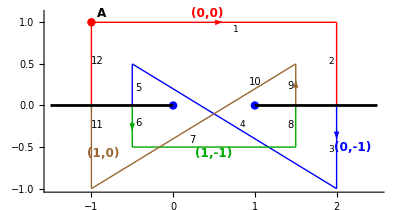

```mathematica
line1={Red,Line[{{-1,1},{2,1}}]};
line2={Red,Line[{{2,1},{2,0}}]};
line3={Blue,Line[{{2,0},{2,-1}}]};
line4={Blue,Line[{{2,-1},{-1/2,1/2}}]};
line5={Blue,Line[{{-1/2,1/2},{-1/2,0}}]};
line6={Darker@Green,Line[{{-1/2,0},{-1/2,-1/2}}]};
line7={Darker@Green,Line[{{-1/2,-1/2},{3/2,-1/2}}]};
line8={Darker@Green,Line[{{3/2,-1/2},{3/2,0}}]};
line9={Brown,Line[{{3/2,0},{3/2,1/2}}]};
line10={Brown,Line[{{3/2,1/2},{-1,-1}}]};
line11={Brown,Line[{{-1,-1},{-1,0}}]};
line12={Red,Line[{{-1,0},{-1,1}}]};
text1=Text[Style["(0,0)",Bold,Red,12],{0.42,1.1}];
text2=Text[Style["(0,-1)",Bold,Blue,12],{2.2,-0.5}];
text3=Text[Style["(1,-1)",Bold,Darker@Green,12],{0.5,-0.58}];
text4=Text[Style["(1,0)",Bold,Brown,12],{-0.85,-0.58}];
arrow1={Arrowheads[0.04],Red,Arrow[{{0.5,1},{0.6,1}}]};
arrow2={Arrowheads[0.04],Blue,Arrow[{{2,-0.3},{2,-0.4}}]};
greenArrow={Arrowheads[0.04],Darker@Green,Arrow[{{-0.5,-0.2},{-0.5,-0.3}}]};
brownArrow={Arrowheads[0.04],Brown,Arrow[{{1.5,0.2},{1.5,0.3}}]};
s1PointG={PointSize[0.015],Blue,Point[{0,0}]};
s2PointG={PointSize[0.015],Blue,Point[{1,0}]};
bcOneG={Thickness[0.005],Line[{{1,0},{2.5,0}}]};
bcTwoG={Thickness[0.005],Line[{{0,0},{-1.5,0}}]};
textAG=Text[Style["A",Black,Bold,12],{-.88,1.1}];
rPointG={PointSize[0.015],Red,Point[{-1,1}]};
leg1G=Text[Style["1",9],{0.77,0.91}];
leg2G=Text[Style["2",9],{1.93,0.53}];
leg3G=Text[Style["3",9],{1.93,-0.53}];
leg4G=Text[Style["4",9],{0.85,-0.23}];
leg5G=Text[Style["5",10],{-0.43,0.21}];
leg6G=Text[Style["6",10],{-0.43,-0.21}];
leg7G=Text[Style["7",10],{0.24,-0.41}];
leg8G=Text[Style["8",10],{1.44,-0.24}];
leg9G=Text[Style["9",10],{1.44,0.24}];
leg10G=Text[Style["10",10],{1,0.28}];
leg11G=Text[Style["11",10],{-0.93,-0.23}];
leg12G=Text[Style["12",10],{-0.93,0.53}];

Show[Graphics@{line1,line2,line3,line4,line5,line6,line7,line8,line9,line10,line11,line12,text1,text2,text3,text4,arrow1,arrow2,greenArrow,brownArrow,s1PointG,s2PointG,bcOneG,bcTwoG,textAG,rPointG,leg1G,leg2G,leg3G,leg4G,leg5G,leg6G,leg7G,leg8G,leg9G,leg10G,leg11G,leg12G},PlotRange->All,Axes->True]
```

```mathematica
zeroOffset=0
oneOffset=0;
wp=50;
logVal1=NIntegrate[H[z,0,0],{z,-1/2+I,3/2+I},WorkingPrecision->wp];
logVal2=NIntegrate[H[z,0,0],{z,3/2+I,3/2},WorkingPrecision->wp];

logVal3=-NIntegrate[H[z,0,-1],{z,3/2-I,3/2},WorkingPrecision->wp];
logVal4=NIntegrate[H[z,0,-1],{z,3/2-I,-1/4+I},WorkingPrecision->wp];
logVal5=NIntegrate[H[z,0,-1],{z,-1/4+I,-1/4},WorkingPrecision->wp];

logVal6=-NIntegrate[H[z,1,-1],{z,-1/4-I,-1/4},WorkingPrecision->wp];
logVal7=NIntegrate[H[z,1,-1],{z,-1/4-I,3/2-I},WorkingPrecision->wp];
logVal8=NIntegrate[H[z,1,-1],{z,3/2-I,3/2},WorkingPrecision->wp];

logVal9=-NIntegrate[H[z,1,0],{z,3/2+I,3/2},WorkingPrecision->wp];
logVal10=NIntegrate[H[z,1,0],{z,3/2+I,-1/2-I},WorkingPrecision->wp];
logVal11=NIntegrate[H[z,1,0],{z,-1/2-I,-1/2},WorkingPrecision->wp];

logVal12=-NIntegrate[logF[z,0,0],{z,-1/2+I,-1/2},WorkingPrecision->wp];
HSol=logVal1+logVal2+logVal3+logVal4+logVal5+logVal6+logVal7+logVal8+logVal9+logVal10+logVal11+logVal12



contourValue2=HSol/(Exp[2 Pi I zeroOffset theAlpha]Exp[2 Pi I oneOffset theBeta](1-Exp[2 Pi I theAlpha])(1-Exp[
-2Pi I theBeta ]));

betaValue=Beta[theAlpha,theBeta];
Print["Beta value: ",N[betaValue,wp]];
Print["Contour value: ",contourValue2];
Abs[betaValue-contourValue2]
betaValue//N
```

0

0.001072651972041569801031961938869274941919243013-0.012864097152789992537489804173543297158374625056 ⅈ

Beta value: 0.99999976055271890394534623730383782689724968357751+0.0005848653573909358712635271055217426012853165613 ⅈ

Contour value: 0.99999976055271890394534623730383782689724968358+0.0005848653573909358712635271055217426012853166 ⅈ

0.

1.+0.000584865 ⅈ

## Section 6: 4-leg Pochhammer contour

1/2

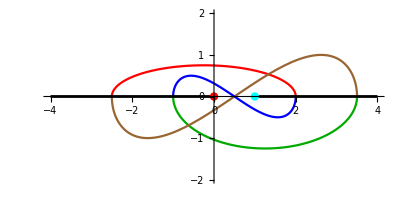

```mathematica
theK=1/2
theK=1/2;
p2=ParametricPlot[{2.25Cos[t]-0.25,0.75 Sin[t]},{t,0,Pi},AxesLabel->{"x","y"},PlotStyle->Red];
p4=ParametricPlot[ReIm[(1.5Sin[t]+1/2)+I(Sin[t] Cos[t])],{t,-3Pi/2,-Pi/2},AxesLabel->{"x","y"},PlotRange->4,PlotStyle->Blue];

p1=ParametricPlot[{2.25Cos[t]+1.25,1.25 Sin[t]},{t,Pi,2 Pi},AxesLabel->{"x","y"},PlotStyle->Darker@Green];

p3=ParametricPlot[ReIm[(3Sin[t]+theK)+2I(Sin[t] Cos[t])],{t,-Pi/2,Pi/2},AxesLabel->{"x","y"},PlotRange->4,PlotStyle->Brown];
theK2=1/2;

line1=Graphics@{Thickness[0.005],Black,Line[{{1,0},{4,0}}]};
line2=Graphics@{Thickness[0.005],Black,Line[{{-4,0},{0,0}}]};
s1PointG=Graphics@{PointSize[0.015],Red,Point[{0,0}]};
s2PointG=Graphics@{PointSize[0.015],Cyan,Point[{1,0}]};
Show[{p1,p2,p3,p4,line1,line2,s1PointG,s2PointG},PlotRange->{{-4,4},{-2,2}},AxesLabel->None,PlotRangePadding->None]
```

```mathematica
p3=ParametricPlot[ReIm[(3Sin[t]+theK)+2I(Sin[t] Cos[t])],{t,-Pi/2,Pi/2},AxesLabel->{"x","y"},PlotRange->4,PlotStyle->Yellow];
blueMin[t_]:=(2.25Cos[Pi-t]-0.25)+I 0.75 Sin[Pi-t];
greenMin[t_]:=(1.5Sin[t]+1/2)+I(Sin[t] Cos[t]);
redMin[t_]:=(2.25Cos[t]+1.25)+I 1.25 Sin[t];
yellowMin[t_]:=(3Sin[t]+1/2)+2I(Sin[t] Cos[t]);

AbsoluteTiming[blueInt= NIntegrate[H[blueMin[t],0,0] D[blueMin[t],t],{t,0,Pi}];
greenInt= NIntegrate[H[greenMin[t],0,-1] D[greenMin[t],t],{t,-3 Pi/2,-Pi/2}];
redInt= NIntegrate[H[redMin[t],1,-1] D[redMin[t],t],{t,Pi,2 Pi}];
yellowInt=-NIntegrate[H[yellowMin[t],1,0] D[yellowMin[t],t],{t,-Pi/2,Pi/2}];
]

AbsoluteTiming[Beta[theAlpha,theBeta]//N]
1/((1-Exp[2 Pi I theAlpha])(1-Exp[-2 Pi I theBeta]))(blueInt+greenInt+redInt+yellowInt)
```

{0.12016,Null}

{0.0000268,1.+0.000584865 ⅈ}

1.+0.000584892 ⅈ

```mathematica
theJ=0
theK=0
opac=0.55;
plotJK=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK]}/.z->1/2+r Exp[I t],{r,0,4},{t,-Pi,0},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[opac],branchColors[[12]]},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
plotJKB=ParametricPlot3D[{Re@z,Im@z,reim@H[z,theJ,theK]}/.z->1/2+r Exp[I t],{r,0,4},{t,0,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[opac],branchColors[[12]]},RegionFunction->Function[{x,y,z},x^2+y^2>=0.01 && (1-x)^2+y^2>=0.01]];
blueTrace=ParametricPlot3D[{Re@z,Im@z,reim@H[blueMin[t],0,0]}/.z->blueMin[t],{t,0,Pi},PlotStyle->Blue];
greenTrace=ParametricPlot3D[{Re@z,Im@z,reim@H[greenMin[t],0,-1]}/.z->greenMin[t],{t,-3 Pi/2,-Pi/2},PlotStyle->Green,PlotRange->3]
redTrace=ParametricPlot3D[{Re@z,Im@z,reim@H[redMin[t],1,-1]}/.z->redMin[t],{t,Pi,2 Pi},PlotStyle->Red];


yellowTrace=ParametricPlot3D[{Re@z,Im@z,reim@H[yellowMin[t],1,0]}/.z->yellowMin[t],{t,-Pi/2,Pi/2},PlotStyle->Yellow];


Show[{plotJK,plotJKB,blueTrace,greenTrace,redTrace,yellowTrace},PlotRange->All]
```

0

0

-Graphics3D-

-Graphics3D-

```mathematica
Manipulate[
ParametricPlot[{2.25Cos[Pi-t]-0.25,0.75 Sin[Pi-t]},{t,0,tEnd},AxesLabel->{"x","y"},PlotStyle->Blue,PlotRange->4],
{{tEnd,0+0.01},0,Pi}
]
```

```mathematica
Manipulate[
ParametricPlot[ReIm[(2.25Cos[t]+1.25)+I 1.25 Sin[t]],{t,Pi,tEnd},AxesLabel->{"x","y"},PlotRange->4,PlotStyle->Red],
{{tEnd,Pi+0.01},Pi,2 Pi}
]
```

```mathematica
Manipulate[
ParametricPlot[ReIm[(1.5Sin[t]+theK)+I(Sin[t] Cos[t])],{t,-3Pi/2,tEnd},AxesLabel->{"x","y"},PlotRange->4,PlotStyle->Darker@Green],
{{tEnd,-3 Pi/2+0.01},-3 Pi/2,-Pi/2}
]
```

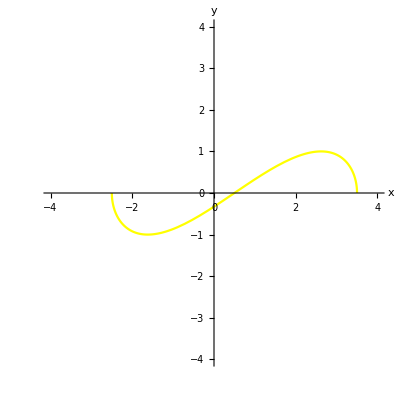

```mathematica
p3=ParametricPlot[ReIm[(3Sin[t]+theK)+2I(Sin[t] Cos[t])],{t,-Pi/2,Pi/2},AxesLabel->{"x","y"},PlotRange->4,PlotStyle->Yellow]
```

```mathematica
Manipulate[
ParametricPlot[ReIm[(3Sin[t]+theK)+2I(Sin[t] Cos[t])],{t,-Pi/2,tEnd},AxesLabel->{"x","y"},PlotRange->4,PlotStyle->Yellow],
{{tEnd,-Pi/2+0.01}, -Pi/2,+Pi/2}
]
```

## Using H[z,k;j] to compute contour integral

```mathematica
zeroOffset=0
oneOffset=0;
logVal1=NIntegrate[H[z,0,0],{z,-1/2+I,3/2+I},WorkingPrecision->25];
logVal2=NIntegrate[H[z,0,0],{z,3/2+I,3/2},WorkingPrecision->25];

logVal3=-NIntegrate[H[z,0,-1],{z,3/2-I,3/2},WorkingPrecision->25];
logVal4=NIntegrate[H[z,0,-1],{z,3/2-I,-1/4+I},WorkingPrecision->25];
logVal5=NIntegrate[H[z,0,-1],{z,-1/4+I,-1/4},WorkingPrecision->25];

logVal6=-NIntegrate[H[z,1,-1],{z,-1/4-I,-1/4},WorkingPrecision->25];
logVal7=NIntegrate[H[z,1,-1],{z,-1/4-I,3/2-I},WorkingPrecision->25];
logVal8=NIntegrate[H[z,1,-1],{z,3/2-I,3/2},WorkingPrecision->25];

logVal9=-NIntegrate[H[z,1,0],{z,3/2+I,3/2},WorkingPrecision->25];
logVal10=NIntegrate[H[z,1,0],{z,3/2+I,-1/2-I},WorkingPrecision->25];
logVal11=NIntegrate[H[z,1,0],{z,-1/2-I,-1/2},WorkingPrecision->25];

logVal12=-NIntegrate[logF[z,0,0],{z,-1/2+I,-1/2},WorkingPrecision->25];
HSol=logVal1+logVal2+logVal3+logVal4+logVal5+logVal6+logVal7+logVal8+logVal9+logVal10+logVal11+logVal12



contourValue2=HSol/(Exp[2 Pi I zeroOffset theAlpha]Exp[2 Pi I oneOffset theBeta](1-Exp[2 Pi I theAlpha])(1-Exp[
-2Pi I theBeta ]));

betaValue=Beta[theAlpha,theBeta];
Print["Beta value: ",betaValue//N];
Print["Contour value: ",contourValue];
Abs[betaValue-contourValue2]
betaValue//N
```

0

0.00107265197204156980103-0.01286409715278999253749 ⅈ

Beta value: 1.+0.000584865 ⅈ

Contour value: 0.999999759429069230557+0.00058484541249248562 ⅈ

0.

1.+0.000584865 ⅈ

## Using logF to compute contours without negative direction at branch cuts

```mathematica
wp=100;
AbsoluteTiming[
 logVal1=NIntegrate[logF[z,0,0],{z,-1/2+I,3/2+I},WorkingPrecision->wp];
logVal2=NIntegrate[logF[z,0,0],{z,3/2+I,3/2},WorkingPrecision->wp];

logVal3=NIntegrate[logF[z,0,-1],{z,3/2,3/2-I},WorkingPrecision->wp];
logVal4=NIntegrate[logF[z,0,-1],{z,3/2-I,-1/4+I},WorkingPrecision->wp];
logVal5=NIntegrate[logF[z,0,-1],{z,-1/4+I,-1/4},WorkingPrecision->wp];

logVal6=NIntegrate[logF[z,1,-1],{z,-1/4,-1/4-I},WorkingPrecision->wp];
logVal7=NIntegrate[logF[z,1,-1],{z,-1/4-I,3/2-I},WorkingPrecision->wp];
logVal8=NIntegrate[logF[z,1,-1],{z,3/2-I,3/2},WorkingPrecision->wp];

logVal9=NIntegrate[logF[z,1,0],{z,3/2,3/2+I},WorkingPrecision->wp];
logVal10=NIntegrate[logF[z,1,0],{z,3/2+I,-1/2-I},WorkingPrecision->wp];
logVal11=NIntegrate[logF[z,1,0],{z,-1/2-I,-1/2},WorkingPrecision->wp];

logVal12=-NIntegrate[logF[z,0,0],{z,-1/2+I,-1/2},WorkingPrecision->wp];
logSol=logVal1+logVal2+logVal3+logVal4+logVal5+logVal6+logVal7+logVal8+logVal9+logVal10+logVal11+logVal12;

contourValue2=logSol/(Exp[2 Pi I zeroOffset theAlpha]Exp[2 Pi I oneOffset theBeta](1-Exp[2 Pi I theAlpha])(1-Exp[
-2Pi I theBeta ]));

betaValue=Beta[theAlpha,theBeta];
Print["Error: ",Abs[betaValue-contourValue2]];]
```

Error: 0.

{1.21501,Null}

## Initialization

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"..","config.wl"}]];
colorNumbers=Join[{14,60,45,57,24,35,43,45,32,16,32,15,17,2,7,3,14,18,21,60,45,57,21,35,43,45,32,16,32,15,17,19,12,37,49,15,7,9,13},Range[42]];

theColorList=Table[ColorData[colorNumbers[[i]],"ColorList"],{i,1,Length[colorNumbers]}];
(*theRGBColors=theColorList/.GrayLevel[azz__]->ColorConvert[GrayLevel[azz],"RGB"];
mycolors=theRGBColors/.RGBColor[az_,bz_,cz_]-> {az,bz,cz};
*)
branchColors=Join[{Red,Blue,Darker@Green,Darker@Yellow,Purple,Orange,Magenta,Pink},Flatten@theColorList[[5;;10]]];

branchColorTable=MapThread[{#1,#2}&,{Range[Length@branchColors], branchColors}];
colors= branchColorTable[[All,2]];
```

### polishValue

```mathematica
polishValue[zVal_,wVal_,wp_]:=Module[{wTemp,difArray,wPos,eqnPrecision},
eqnPrecision=Floor@Precision@(theFunction==0/.z->zVal);
(*Print["eqnPrecision: ",eqnPrecision];*)
 wTemp=w/.NSolve[theFunction==0/.z->zVal,w,WorkingPrecision->eqnPrecision];
(*Print["wTemp: ",wTemp];*)
difArray=Abs[wVal-#]&/@ wTemp;
(*Print["difArray: ",difArray//N];*)
wPos=Position[difArray,Min@difArray][[1,1]];
If[difArray[[wPos]]>10^-9,
Print[Style["polishValue: min dif array>10^-9",Red]];
Print["  difArray: ",N[difArray,10]];
];
wTemp[[wPos]]
];
```

### getLogContour

```mathematica
Options[getLogContour]={"wp"->MachinePrecision,"ag"->MachinePrecision};
  getLogContour[contourF_,tStart_,tEnd_,color_,log0WStart_,log1WStart_,z1_,z2_,type_,OptionsPattern[]]:=Module[{log0Deriv,log0Sol,log0WEnd,log1Deriv,log1Sol,contourBetaF,contourLogPlot,contourVal,log1WEnd},
(*
 do log0 trace
*)
log0Deriv=w'[t]==(1/contourF[t] D[contourF[t],t]);
log0Sol=NDSolveValue[{log0Deriv,w[tStart]==log0WStart},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->OptionValue["wp"]];
Print["Precision of log0Sol: ",Precision@log0Sol];
log0WEnd=log0Sol[tEnd];
(*
 do log around z=1 log1Deriv,log1WStart,log1Sol,log1WEnd
*)
log1Deriv=w'[t]==(-1/(1-contourF[t]) D[contourF[t],t]);
log1Sol=NDSolveValue[{log1Deriv,w[tStart]==log1WStart},w,{t,tStart,tEnd},WorkingPrecision->OptionValue["wp"],AccuracyGoal->OptionValue["ag"]];
Print["Precision of log1Sol: ",Precision@log1Sol];
log1WEnd=log1Sol[tEnd];
(*
 now compute integral over leg 
*)
 contourBetaF[t_]:=(Exp[z1 log0Sol[t]] Exp[z2 log1Sol[t]]);

contourLogPlot=ParametricPlot3D[{Re@z,Im@z,type@contourBetaF[t]}/.z->contourF[t],{t,tStart,tEnd},PlotStyle->color,BoxRatios->{1, 1, 1}];

contourVal=NIntegrate[contourBetaF[t] D[contourF[t],t],{t,tStart,tEnd}(*Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"}*),AccuracyGoal->OptionValue["ag"],WorkingPrecision->OptionValue["wp"],MaxRecursion->300];

(*NIntegrate[ polishMedial[t,rationalRNorm,implicitF,lowPrecMedialSol[t],$preciseAnalyticPolishPrecision](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->$preciseAnalyticPolishPrecision,AccuracyGoal->$preciseAnalyticPolishPrecision/2,MaxRecursion->Infinity],
*)

{contourBetaF,contourLogPlot,contourVal,log0WEnd,log1WEnd}

]
```

### getLogContourTract

```mathematica
getLogContourTract[contourF_,tStart_,tEnd_,color_,log0WStart_,log1WStart_,z1_,z2_,type_]:=Module[{log0Deriv,log0Sol,log0WEnd,log1Deriv,log1Sol,contourBetaF,contourLogPlot,contourVal,log1WEnd,tractPoints},
(*
 do log0 trace
*)
log0Deriv=w'[t]==(1/contourF[t] D[contourF[t],t]);
log0Sol=NDSolveValue[{log0Deriv,w[tStart]==log0WStart},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->1/1000];
log0WEnd=log0Sol[tEnd];
(*
 do log around z=1 log1Deriv,log1WStart,log1Sol,log1WEnd
*)
log1Deriv=w'[t]==(-1/(1-contourF[t]) D[contourF[t],t]);
log1Sol=NDSolveValue[{log1Deriv,w[tStart]==log1WStart},w,{t,tStart,tEnd}];
log1WEnd=log1Sol[tEnd];
(*
 now compute integral over leg 
*)
 contourBetaF[t_]:=(Exp[z1 log0Sol[t]] Exp[z2 log1Sol[t]]);

contourLogPlot=ParametricPlot3D[{Re@z,Im@z,type@contourBetaF[t]}/.z->contourF[t],{t,tStart,tEnd},PlotStyle->color,BoxRatios->{1, 1, 1}];
tractPoints=Table[{Re@contourF[t],Im@contourF[t],type@contourBetaF[t]},{t,tStart,tEnd,(tEnd-tStart)/10}];

contourVal=NIntegrate[contourBetaF[t] D[contourF[t],t],{t,tStart,tEnd}];
{contourBetaF,contourLogPlot,contourVal,log0WEnd,log1WEnd,tractPoints}

]
```

### Set up file names

```mathematica
realPlotDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"\\realBetaPlot"<>StringTake[testCase,-4;;]<>".m"}];
  imagPlotDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase<>"\\imagBetaPlot"<>StringTake[testCase,-4;;]<>".m"}];
   singularDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"singularData.m"}] ;
seriesFileName[testCase_String,k_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\"<>"`2`series.m"][testCase,ToString@k]}];

annularMonodromyFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"\\annularMonodromies.m"}];
annularMonodromyTableFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"\\annularMonodromyTableFileName.m"}]; 
annularMonodromyTableGraphicsFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"\\annularMonodromyTableGraphics.jpg"}]; 

 singularMonodromyFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"\\singularMonodromies.m"}];
summatorySeriesFileName[testCase_String,k_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\"<>"`2`summatorySeries.m"][testCase,ToString@k]}];
```